```mathematica
sol = DSolve[{Tan[x] y[x]+y'[x]==sin[2 x],y[0] == 2},y[x],x]
```

{{y[x]→2 Cos[x]+Cos[x] Sec[K[1]] sin[2 K[1]]K[1]0x}}

```mathematica
y[x] /. First[sol]
```

2 Cos[x]+Cos[x] Sec[K[1]] sin[2 K[1]]K[1]0x

```mathematica
DSolve[{Tan[x] y[x]+y'[x]==Sin[2 x],y[0] == 2},y[x],x]
```

{{y[x]→-2 (-2 Cos[x]+Cos[x]^2)}}

```mathematica
{{y[x]->-2 (-2 Cos[x]+Cos[x]^2)}}
a=1
b=2
c=3
```

{{y[x]→-2 (-2 Cos[x]+Cos[x]^2)}}

1

2

3

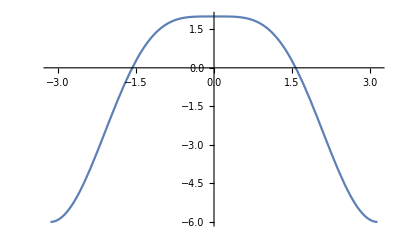

```mathematica
Plot[
Evaluate[
y[x]/. First[DSolve[{Tan[x] y[x]+y'[x]==Sin[2 x],y[0] == 2},y[x],x]]],{x, -Pi, Pi}]
```

```mathematica
sol1 = DSolve[{a*y''[t] + b*y'[t] + c*y[t]== 0}, y[t], t]
```

{{y[t]→ⅇ^-t C[2] Cos[√2 t]+ⅇ^-t C[1] Sin[√2 t]}}

```mathematica
Manipulate[
Plot[
Evaluate[
y[t] /.First[
DSolve[{a*y''[t] + b*y'[t] + c*y[t]== 0,y[0] == 1, y'[1]==0}, y[t], t]]],{t,-10,10}],{a,0,10},{b,0,10},{c,0,10}]
```

```mathematica
DSolve[{y'[t]^2 + y[t]== a}, y[t], t]
```

{{y[t]→1/4 (4-t^2-2 t C[1]-C[1]^2)},{y[t]→1/4 (4-t^2+2 t C[1]-C[1]^2)}}

```mathematica
Manipulate[
Plot[
Evaluate[
y[t] /.First[
DSolve[{y'[t]^2 + y[t]== a, y[0]==b}, y[t], t]]],{t,-10,10}],{a,-10,10},{b,-10,10}]
```

```mathematica
DSolve[{y[t]^2 + y'[t]== a}, y[t], t]
```

{{y[t]→(ⅇ^(2 t)-ⅇ^(2 C[1]))/(ⅇ^(2 t)+ⅇ^(2 C[1]))}}

```mathematica
Manipulate[
Plot[
Evaluate[
y[t] /.First[
DSolve[{y[t]^2 + y'[t]== a, y[0]==b}, y[t], t]]],{t,-1,1}],{a,-10,10},{b,-10,10}]
```

```mathematica
s= NDSolve[{x''[t] + 0.1*x'[t] + x[t] +x[t]^3==10*Cos[1.3*t],x'[0] == 1, x[0]==0},x[t],{t,0, 100}]
```

{{x[t]→InterpolatingFunction[…][t]}}

```mathematica
Manipulate[s=NDSolve[{D[x'[t],t]+g*x'[t]+x[t]-a*x[t]^3==f*Cos[w*t],x[0]==1,x'[0]==0},x[t],{t,-10,10}];
ParametricPlot[Evaluate[{t,x[t]}/.s],{t,-10,10}],{g,0,10},{f,0,10},{a,-1,1},{w,0.5,1.5,0.5}]
```

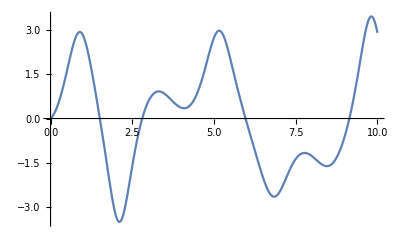

```mathematica
Plot[x[t]/.s,{t,0,10}]
```

```mathematica
AsymptoticDSolveValue[{x''[t] + w^2*x[t] + e*b*x [t]^3 == 0, x[0] ==a,  x'[0] == 0 }, x, {t, 0, 5}]
```

1+1/2 t^2 (-2 e-w^2)+1/24 t^4 (12 e^2+8 e w^2+w^4)

```mathematica
AsymptoticDSolveValue[{x''[t] + 1^2*x[t] + 1/100*4*x [t]^3 == 0, x[0] ==2, x'[0] == 0 }, x, {t, 0, 5}]
```

2-(29 t^2)/25+(1073 t^4)/7500

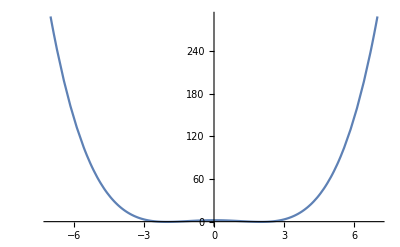

```mathematica
Plot[2-(29 t^2)/25+(1073 t^4)/7500,{t,-7,7}]
```

```mathematica
s= NDSolve[{x''[t] + 1^2*x[t] + 1/100*4*x [t]^3 == 0, x[0] ==2, x'[0] == 0 },x, {t, 0, 5}]
```

{{x→InterpolatingFunction[…]}}

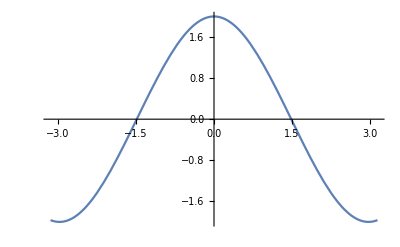

```mathematica
Plot[
Evaluate[
x[t]/. First[DSolve[{x''[t] + 1^2*x[t] + 1/100*4*x [t]^3 == 0, x[0] ==2, x'[0] == 0},x[t],t]]],{t, -Pi, Pi}]
```

```mathematica
AsymptoticDSolveValue[{x''[t] + w^2*x[t] - e*b*x [t]^2 == 0, x[0] ==0,  x'[0] == v}, x, {t, 0, 5}]
```

t v+1/12 b e t^4 v^2-1/6 t^3 v w^2+1/120 t^5 v w^4

```mathematica
AsymptoticDSolveValue[{x''[t] + 1^2*x[t] - 1/100*4*x [t]^2 == 0, x[0] ==0,  x'[0] == 2}, x, {t, 0, 5}]
```

2 t-t^3/3+t^4/75+t^5/60

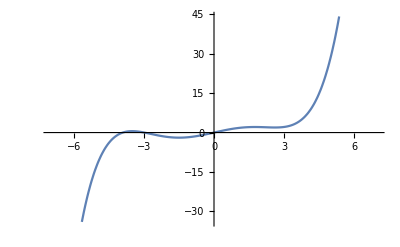

```mathematica
Plot[2 t-t^3/3+t^4/75+t^5/60,{t,-7,7}]
```

```mathematica
s= NDSolve[{x''[t] + 1^2*x[t] - 1/100*4*x [t]^2 == 0, x[0] ==0,  x'[0] == 2}, x, {t, 0, 5}]
```

{{x→InterpolatingFunction[…]}}

NDSolve::derlen: The length of the derivative operator Derivative[1] in x'[t] is not the same as the number of arguments.